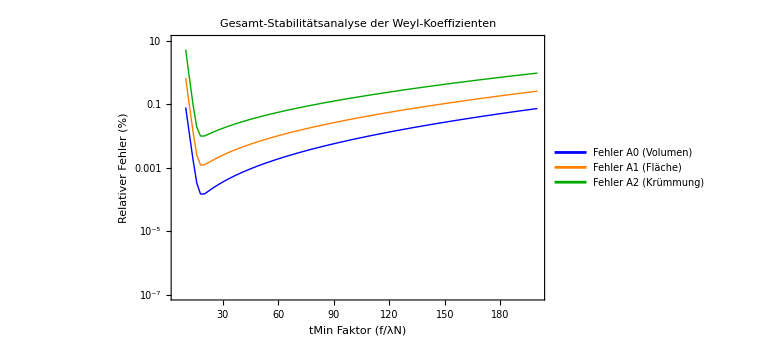

Koeffizient | Plateau-Mittel | Theorie | Fehler %
A0 (Volumen) | 0.0582521 | 0.0582597 | -0.0130413
A1 (Fläche) | -0.288313 | -0.288468 | -0.053779
A2 (Krümmung) | 0.121304 | 0.121585 | -0.231853

```mathematica
ClearAll["Global`*"];

(*1. Daten laden*)
path="C:/Users/sulta/git/cone-operator-lab/data/eigenvalues/box_eigs_exact_20000.txt";
allEigs=Sort@Select[Flatten@Import[path,"Table"]//N,#>0&];
nUse=20000;
eigs=allEigs[[1;;nUse]];
λN=Last[eigs];

(*2. Theorie (Exakte Weyl-Referenz)*)
{a,b,c}={1.0,1.5,2.3};
Vtrue=a b c;
Strue=2 (a b+a c+b c);
A0true=Vtrue/(6 Pi^2);
A1true=-Strue/(16 Pi);
alpha2Weyl=(a+b+c)/(8 Sqrt[Pi]);
(* convert alpha2->A2 in the same normalization used in the heat-fit *)
A2Weyl=alpha2Weyl (4 Pi)^(3/2)/(4 Pi^3);
(*3. Scan*)
factors=Range[10,200,2];
scanResults=Table[Module[{tMin,tMax,tGrid,Z,X,coef},tMin=f/λN;
tMax=500/λN;
tGrid=Exp@Subdivide[Log[tMin],Log[tMax],200];
Z=Total[Exp[-Outer[Times,eigs,tGrid]],{1}];
X=Table[t^{-3/2,-1,-1/2,0},{t,tGrid}];
coef=PseudoInverse[X].Z;
{(coef[[1]]*(4 Pi)^(3/2))/(6 Pi^2),coef[[2]],(coef[[3]]*(4 Pi)^(3/2))/(4 Pi^3)}],{f,factors}];

(*4. Fehler (%) berechnen*)
errA0=Abs[scanResults[[All,1]]/A0true-1]*100;
errA1=Abs[scanResults[[All,2]]/A1true-1]*100;
errA2=Abs[scanResults[[All,3]]/A2Weyl-1]*100;

(*5. Plateau-Mittelung (f=80 bis 150)*)
pIdx=Flatten@Position[factors,f_/;80<=f<=150];
means=Mean[scanResults[[pIdx]]];

(*6. Visualisierung mit fixiertem Bereich für alle Kurven*)
ListLogPlot[{Transpose[{factors,errA0}],Transpose[{factors,errA1}],Transpose[{factors,errA2}]},Joined->True,PlotRange->{All,{10^-7,10}},(*Erweitert nach unten,damit Blau/Orange sichtbar werden*)PlotStyle->{Directive[Blue,Thick],Directive[Orange,Thick],Directive[Darker[Green],Thick]},PlotLegends->{"Fehler A0 (Volumen)","Fehler A1 (Fläche)","Fehler A2 (Krümmung)"},Frame->True,FrameLabel->{"tMin Faktor (f/λN)","Relativer Fehler (%)"},PlotLabel->"Gesamt-Stabilitätsanalyse der Weyl-Koeffizienten",GridLines->Automatic,ImageSize->Large]

(*7. Output-Tabelle*)
Print[Grid[{{"Koeffizient","Plateau-Mittel","Theorie","Fehler %"},{"A0 (Volumen)",N[means[[1]],8],N[A0true,8],N[100 (means[[1]]/A0true-1),5]},{"A1 (Fläche)",N[means[[2]],8],N[A1true,8],N[100 (means[[2]]/A1true-1),5]},{"A2 (Krümmung)",N[means[[3]],8],N[A2Weyl,8],N[100 (means[[3]]/A2Weyl-1),5]}},Frame->All,Alignment->Left,Background->{None,{Lighter[Gray,0.9],None}}]];
```